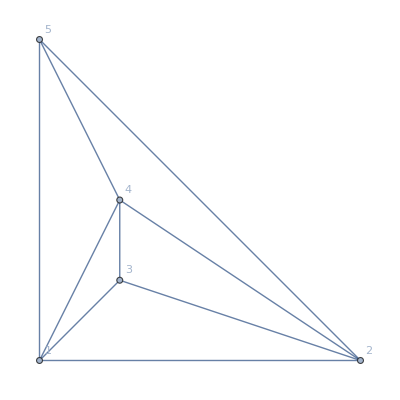

```mathematica
MinimalGraph[4]
```

```mathematica
SymbolLevel[s_]:=StringCount[SymbolName[s],"x"]+1
```

```mathematica
FindFullFormula2[g_]:=FindFullFormula2[g]=FindFullFormula[g]
```

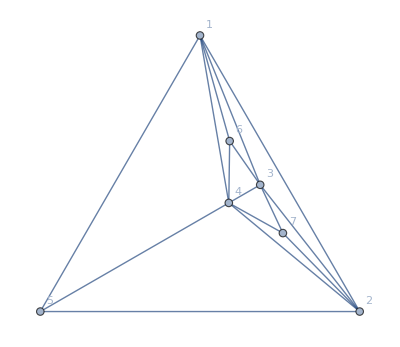

```mathematica
g12=Graph[{1<->2,2<->3,3<->1,4<->1,4<->2,4<->3,5<->4,5<->1,5<->2,6<->1,6<->4,6<->3,7<->4,7<->3,7<->2},GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

```mathematica
IsomorphicGraphQ[gr12,MinimalGraph[6]]
```

False

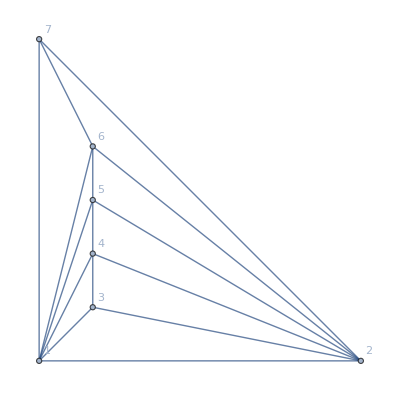

```mathematica
MinimalGraph[6]
```

```mathematica
MaximalPlanarQ[g12]
```

True

```mathematica
BaseGenerators[FindFullFormula2[g12]]
```

<|4→{v17x26x35x4},5→{v1x2x3x4x567,v1x2x35x4x67,v1x26x3x4x57,v17x2x3x4x56}|>

```mathematica
BaseGenerators[FindFullFormula2[MinimalGraph[6]]]
```

<|4→{v1x2x357x46},5→{v1x2x36x4x57,v1x2x36x47x5,v1x2x35x47x6}|>

```mathematica
{Length[FindFullFormula2[g12]],Length[FindFullFormula2[MinimalGraph[6]]]}
```

{15,15}

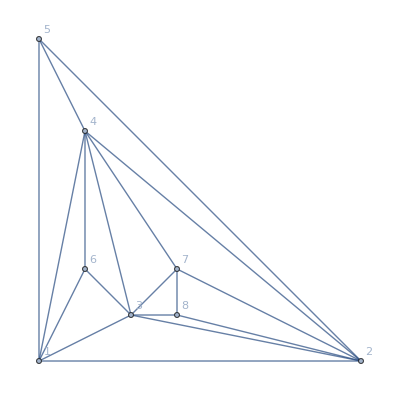

```mathematica
g123=Graph[{1<->2,2<->3,3<->1,4<->1,4<->2,4<->3,5<->4,5<->1,5<->2,6<->1,6<->4,6<->3,7<->4,7<->3,7<->2,7<->8,8<->3,8<->2},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

```mathematica
MaximalPlanarQ[g123]
```

```mathematica
{Length[FindFullFormula2[g123]],Length[FindFullFormula2[MinimalGraph[7]]]}
```

{52,52}

```mathematica
BaseGenerators[FindFullFormula2[g123]]
```

<|4→{v17x26x35x48},5→{v1x2x3x48x567,v1x2x35x48x67,v1x26x3x48x57,v18x2x3x4x567,v18x2x35x4x67,v18x26x3x4x57,v18x26x35x4x7,v17x2x3x4x568,v17x2x3x48x56,v17x2x35x4x68,v17x26x3x4x58},6→{v1x2x3x4x58x67,v1x2x3x4x57x68}|>

```mathematica
FormulaGraph[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s2]->SetsToSymbol[s1]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> SymbolToLabel[ SetsToSymbol[s]],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding"]
]
```

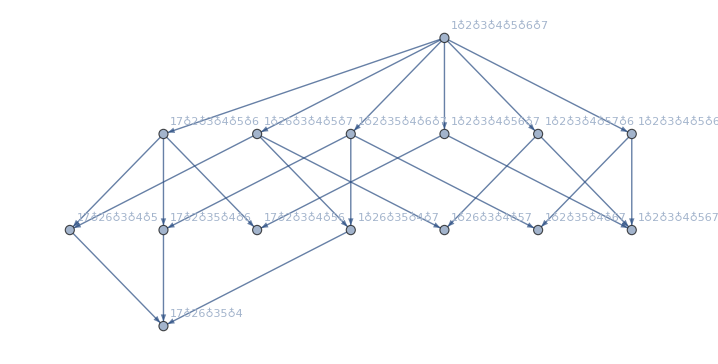

```mathematica
FormulaGraph[FindFullFormula2[g12]]
```

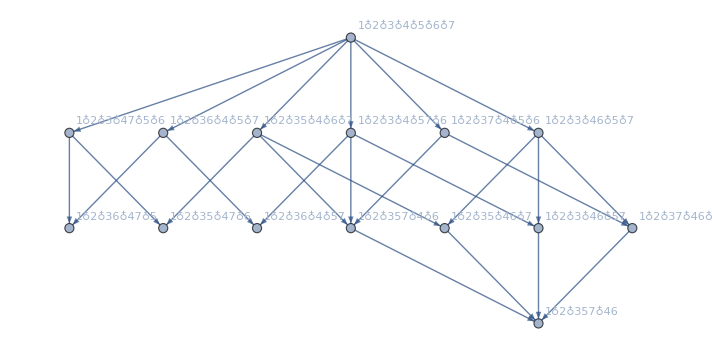

```mathematica
FormulaGraph[FindFullFormula2[MinimalGraph[6]]]
```

```mathematica
Expl[g_]:={VertexCount[g],EdgeCount[g]}
```

```mathematica
Expl[MinimalGraph[6]]
```

{7,15}

```mathematica
Expl[g12]
```

{7,15}

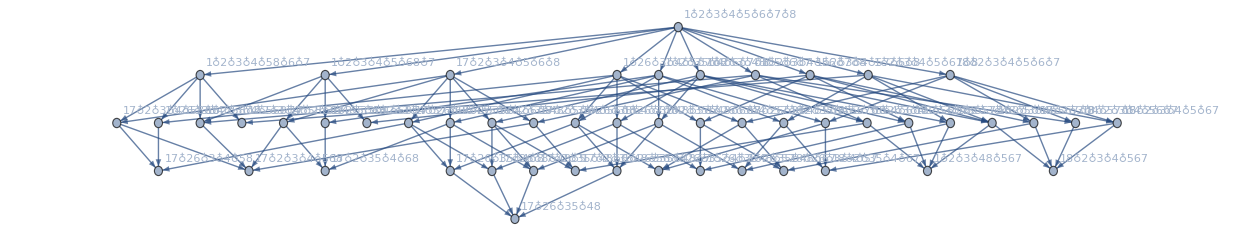

```mathematica
FormulaGraph[FindFullFormula2[g123]]
```

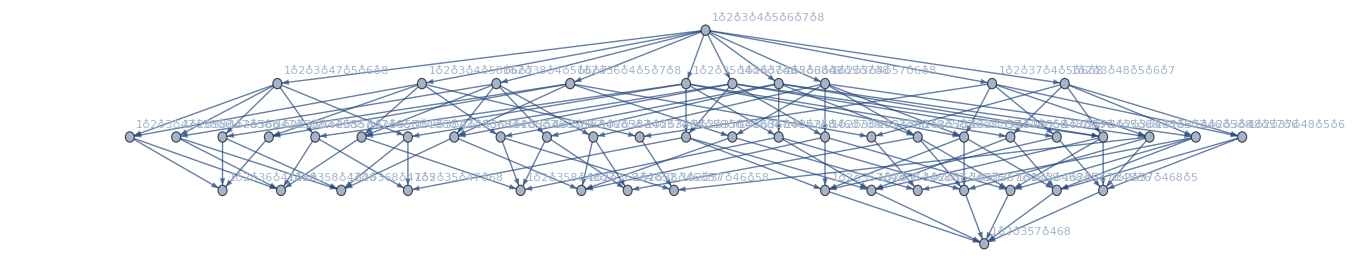

```mathematica
FormulaGraph[FindFullFormula2[MinimalGraph[7]]]
```

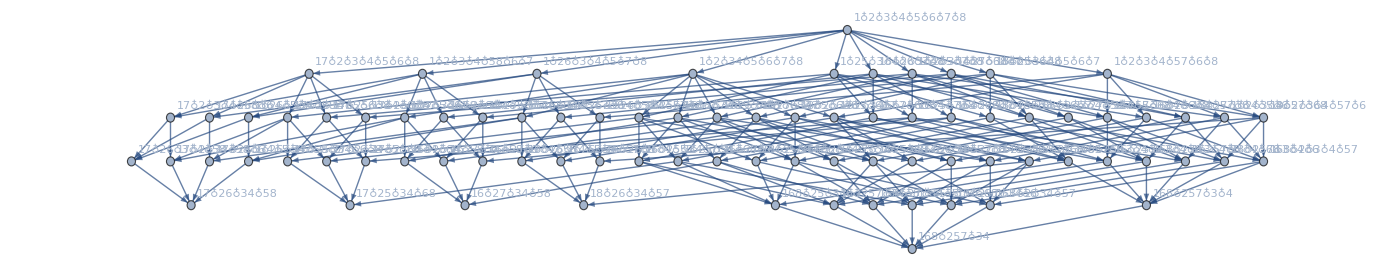

```mathematica
FormulaGraph[FindFullFormula2[JacobsThalGraph[4]]]
```

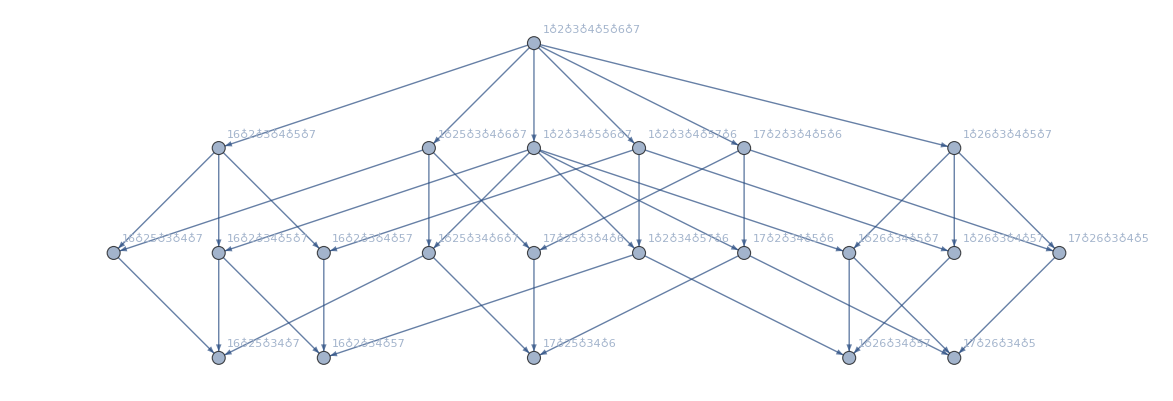

```mathematica
FormulaGraph[FindFullFormula2[JacobsThalGraph[3]]]
```

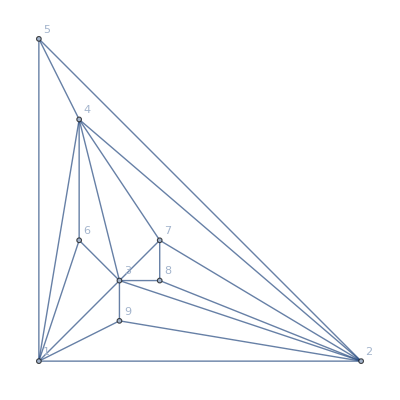

```mathematica
g1234=Graph[{1<->2,2<->3,3<->1,4<->1,4<->2,4<->3,5<->4,5<->1,5<->2,6<->1,6<->4,6<->3,7<->4,7<->3,7<->2,7<->8,8<->3,8<->2,1<->9,9<->3,9<->2},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

```mathematica
Table [Length[Map[SymbolToSets[#]&,Select[FindFullFormula2[g1234],SymbolLevel[#]==level&]]],{level,3,10}]
```

{0,1,31,90,65,15,1,0}

```mathematica
Table [Length[Map[SymbolToSets[#]&,Select[FindFullFormula2[MinimalGraph[8]],SymbolLevel[#]==level&]]],{level,3,10}]
```

{0,1,31,90,65,15,1,0}

```mathematica
BaseGenerators[FindFullFormula2[MinimalGraph[7]]]
```

<|4→{v1x2x357x468},5→{v1x2x38x46x57,v1x2x37x46x58,v1x2x36x48x57,v1x2x36x47x58,v1x2x368x4x57,v1x2x368x47x5,v1x2x35x47x68,v1x2x358x47x6,v1x2x358x46x7}|>

```mathematica
Table [Length[Map[SymbolToSets[#]&,Select[FindFullFormula2[g12],SymbolLevel[#]==level&]]],{level,4,8}]
```

{1,7,6,1,0}

```mathematica
Table [Length[Map[SymbolToSets[#]&,Select[FindFullFormula2[g12],SymbolLevel[#]==level&]]],{level,4,8}]
```

{1,7,6,1,0}

```mathematica
Table [Length[Map[SymbolToSets[#]&,Select[FindFullFormula2[g123],SymbolLevel[#]==level&]]],{level,4,8}]
```

{1,15,25,10,1}

```mathematica
TableForm[Table[Table [Length[Map[SymbolToSets[#]&,Select[FindFullFormula2[MinimalGraph[k]],SymbolLevel[#]==level&]]],{level,4,k+1}],{k,4,12}]]
```

1 | 1 |  |  |  |  |  |  |  | 
1 | 3 | 1 |  |  |  |  |  |  | 
1 | 7 | 6 | 1 |  |  |  |  |  | 
1 | 15 | 25 | 10 | 1 |  |  |  |  | 
1 | 31 | 90 | 65 | 15 | 1 |  |  |  | 
1 | 63 | 301 | 350 | 140 | 21 | 1 |  |  | 
1 | 127 | 966 | 1701 | 1050 | 266 | 28 | 1 |  | 
1 | 255 | 3025 | 7770 | 6951 | 2646 | 462 | 36 | 1 | 
1 | 511 | 9330 | 34105 | 42525 | 22827 | 5880 | 750 | 45 | 1

```mathematica
TableForm[Table[Table [Length[Map[SymbolToSets[#]&,Select[FindFullFormula2[JacobsThalGraph2[k]],SymbolLevel[#]==level&]]],{level,3,k+1}],{k,2,14}]]
```

0 |  |  |  |  |  |  |  |  |  |  |  | 
1 | 0 |  |  |  |  |  |  |  |  |  |  | 
0 | 1 | 0 |  |  |  |  |  |  |  |  |  | 
0 | 1 | 1 | 0 |  |  |  |  |  |  |  |  | 
1 | 3 | 3 | 1 | 0 |  |  |  |  |  |  |  | 
0 | 5 | 10 | 6 | 1 | 0 |  |  |  |  |  |  | 
1 | 11 | 30 | 29 | 10 | 1 | 0 |  |  |  |  |  | 
0 | 21 | 91 | 126 | 70 | 15 | 1 | 0 |  |  |  |  | 
1 | 43 | 273 | 525 | 420 | 146 | 21 | 1 | 0 |  |  |  | 
0 | 85 | 820 | 2142 | 2331 | 1170 | 273 | 28 | 1 | 0 |  |  | 
1 | 171 | 2460 | 8653 | 12390 | 8427 | 2835 | 470 | 36 | 1 | 0 |  | 
0 | 341 | 7381 | 34782 | 64240 | 56925 | 25872 | 6160 | 759 | 45 | 1 | 0 | 
1 | 683 | 22143 | 139469 | 328240 | 369292 | 217602 | 69707 | 12276 | 1165 | 55 | 1 | 0

```mathematica
ChromaticPolynomial[g12,x]
```

162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7

```mathematica
CompleteBaseCoeff[ChromaticPolynomial[g12,x]]
```

{0,0,0,0,1,7,6,1}

```mathematica
Multicolumn[Table[k->Table [Length[Map[SymbolToSets[#]&,Select[FindFullFormula2[MinimalGraph[k]],SymbolLevel[#]==level&]]],{level,4,k}],{k,4,12}]]
```

4→{1} | 7→{1,15,25,10} | 10→{1,127,966,1701,1050,266,28}
5→{1,3} | 8→{1,31,90,65,15} | 11→{1,255,3025,7770,6951,2646,462,36}
6→{1,7,6} | 9→{1,63,301,350,140,21} | 12→{1,511,9330,34105,42525,22827,5880,750,45}

```mathematica
Multicolumn[Table[k->Map[SymbolToLabel2[#,k+1]&,Select[FindFullFormula2[MinimalGraph[k]],SymbolLevel[#]==4&]],{k,4,12}]]
```

4→{35} | 7→{357♁468} | 10→{3579b♁468a}
5→{35♁46} | 8→{3579♁468} | 11→{3579b♁468ac}
6→{357♁46} | 9→{3579♁468a} | 12→{3579bd♁468ac}

```mathematica
Multicolumn[Table[k->Map[SymbolToLabel2[#,k+1]&,Select[FindFullFormula2[MinimalGraph[k]],SymbolLevel[#]==5&]],{k,4,12}]]
```

```mathematica
Multicolumn[Table[k->Max[Map[Length[DirectRefinements[SymbolToSets[#]]]&,Select[FindFullFormula2[JacobsThalGraph[k]],SymbolLevel[#]==4&]]],{k,4,8}]]
```

4→6 | 6→14 | 8→30
5→7 | 7→15 |